```mathematica
SetDirectory[NotebookDirectory[]]
```

\\wsl.localhost\Ubuntu\home\shiyin\work\git\work\Critical-region\QCD\find_Tc\source

```mathematica
fpi=Flatten[Table[Import["./Tem"<>ToString[i]<>"/BUFFER/FPI.DAT"],{i,1,10}]];
T=Flatten[Table[Import["./Tem"<>ToString[i]<>"/BUFFER/T.DAT"],{i,1,10}]];
```

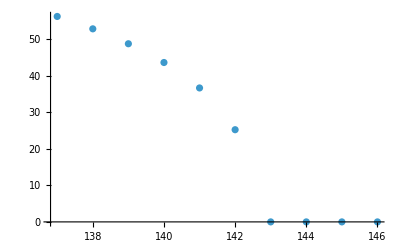

```mathematica
ListPlot[Transpose[{T,fpi}]]
```